# Tools

## Basic Headers—make sure that the “dataDir” is correctly linked

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/gabriele/Documents/GitHub/ML-correlator/Tree classifier for graphs

```mathematica
fourPointDataDir="../consolidated_data";
```

```mathematica
niceTime[timeInSec_]:=If[timeInSec<($TimeUnit/100)||Not[NumericQ[timeInSec]]||Precision[timeInSec]==0,"",Block[{measure=Select[Transpose[{(Quotient[Mod[timeInSec,#1],#2]&@@@Partition[{timeInSec 10,3.15569277216*^7,3600*24.,3600.,60.,1.,10^-3,10.^-6,10.^-9},2,1]),{" years"," days"," hours"," minutes"," seconds"," ms"," μs"," ns"}}],#[[1]]>0&]},If[Length[measure]>0,Row[Row[#,""]&/@measure[[1;;Min[2,Length[measure]]]],", "],""]]];
map[function_,list_]:=If[Length[list]>0,Module[{monitor=0,len=Length[list],newFcn,t00=AbsoluteTime[]},newFcn[i_]:=(monitor=i;function[list[[i]]]);Monitor[Map[newFcn,Range[len]],(Column[{ProgressIndicator[(monitor-1)/len,ImageSize->{1250,30},ImageMargins->0,BaselinePosition->Center],If[monitor≥1,Row[{If[monitor>1,Row[{niceTime[Round[AbsoluteTime[]-t00]]," so far; approx. ",niceTime[Round[((AbsoluteTime[]-t00)/(monitor-1))*(len-monitor+1)]]," remaining."}],"                                              "]," (",monitor-1,"/",len,")"}],""]},Alignment->Left,Spacings->0.1])]],Map[function,list]];
littleGroup[graph_]:=Block[{num=Numerator[graph],den=Denominator[graph]},num=Join@@(Function[{y,z},y&/@Range[z]]@@@FactorList[num][[2;;-1]]);den=Join@@(Function[{y,z},y&/@Range[z]]@@@FactorList[den][[2;;-1]]);-(Count[num,#,{0,∞}]-Count[den,#,{0,∞}])&/@Sort[DeleteDuplicates[Flatten[List@@@Cases[graph,_x,{0,∞}]]]]];
```

## Basic Data Analysis (same as before)

```mathematica
planarGraphDials[loop_]:=Block[{fileName=FileNameJoin[{fourPointDataDir,(("fGraph_dials_"<>ToString[loop]<>".tex"))}]},If[FileExistsQ[fileName],Set[planarGraphDials[loop],ReadList[fileName]],{{}}]];
planarGraphEdges[loop_]:=Block[{fileName=FileNameJoin[{fourPointDataDir,(("fGraph_edges_"<>ToString[loop]<>".tex"))}],raw,rule},If[FileExistsQ[fileName],(raw=ReadList[fileName];rule=Thread[Rule[Range[Binomial[4+loop,2]],Subsets[Range[4+loop],{2}]]];Set[planarGraphEdges[loop],(raw/.rule)]),{{}}]];
fGraphNums[loop_]:=Block[{fileName=FileNameJoin[{fourPointDataDir,("fGraph_nums_"<>ToString[loop]<>".tex")}],raw,rule},If[FileExistsQ[fileName],(raw=ReadList[fileName];rule=Thread[Rule[Range[Binomial[4+loop,2]],Subsets[Range[4+loop],{2}]]];raw=Times@@@#&/@(x@@@#&/@#&/@(raw/.rule));Set[fGraphNums[loop],raw]),{{}}]];
fGraphList[loop_]:=If[FileExistsQ[FileNameJoin[{fourPointDataDir,("fGraph_nums_"<>ToString[loop]<>".tex")}]],Set[fGraphList[loop],(Join@@(fGraphNums[loop](1/(Times@@@(x@@@#&/@planarGraphEdges[loop])))))],{{}}];

amplitudeCoefficients[loop_]:=Block[{fileName=FileNameJoin[{fourPointDataDir,(("amplitudeCoefficients_"<>ToString[loop]<>".tex"))}]},If[FileExistsQ[fileName],Set[amplitudeCoefficients[loop],(<<(fileName))],{}]];
```

```mathematica
FileExistsQ[FileNameJoin[{fourPointDataDir,("fGraph_nums_"<>ToString[6]<>".tex")}]]
```

True

## Graph Analysis (with a few new face-extraction tools)

```mathematica
graphIsomorphisms[fcnList__]/;(Length[{fcnList}]==2):=Block[{factors={fcnList},isoList,bases,nums,baseLabels=DeleteDuplicates[Cases[{fcnList}[[1]],x[y__]:>y,{0,∞}]]},If[Length[DeleteDuplicates[factors]]==1,((bases=(Function[{q},List@@@DeleteDuplicates[Cases[Denominator[q],x[y__],{0,∞}]]]/@factors);nums=(factors*((Times@@(x@@@#))&/@bases));bases=Graph[UndirectedEdge@@@#]&/@bases;isoList=(FindGraphIsomorphism[#1,#2,All]&@@bases);If[Length[isoList]==0,{},(isoList=(Function[{iso},Thread[Rule@@(baseLabels/.{{},iso})]]/@isoList);isoList=Select[isoList,SameQ[nums[[2]],(nums[[1]]/.{x[y__]:>(x@@Sort[{y}/.#])})]&])])),(Which[Not[SameQ@@(LeafCount/@factors)],{},True,(bases=(Function[{q},List@@@DeleteDuplicates[Cases[Denominator[q],x[y__],{0,∞}]]]/@factors);nums=(factors*((Times@@(x@@@#))&/@bases));bases=Graph[UndirectedEdge@@@#]&/@bases;isoList=(FindGraphIsomorphism[#1,#2,All]&@@bases);If[Length[isoList]==0,{},(isoList=(Function[{iso},Thread[Rule@@(baseLabels/.{{},iso})]]/@isoList);isoList=Select[isoList,SameQ[nums[[2]],(nums[[1]]/.{x[y__]:>(x@@Sort[{y}/.#])})]&])])])]];
graphIsomorphism[fcnList__]/;(Length[{fcnList}]==2):=Block[{factors={fcnList},isoList,bases,nums,baseLabels=DeleteDuplicates[Cases[{fcnList}[[1]],x[y__]:>y,{0,∞}]]},If[Length[DeleteDuplicates[factors]]==1,Thread[Rule[baseLabels,baseLabels]],(Which[Not[SameQ@@(LeafCount/@factors)],{},True,(bases=(Function[{q},List@@@DeleteDuplicates[Cases[Denominator[q],x[y__],{0,∞}]]]/@factors);nums=(factors*((Times@@(x@@@#))&/@bases));bases=Graph[UndirectedEdge@@@#]&/@bases;isoList=(FindGraphIsomorphism[#1,#2,All]&@@bases);If[Length[isoList]==0,{},(isoList=(Function[{iso},Thread[Rule@@(baseLabels/.{{},iso})]]/@isoList);isoList=Select[isoList,SameQ[nums[[2]],(nums[[1]]/.{x[y__]:>(x@@Sort[{y}/.#])})]&,1])])])]];
graphEquivalentQ[fcnList__]/;(Length[{fcnList}]==2):=Not[graphIsomorphism[fcnList]==={}];
distinctGraphs[seedList_]:=DeleteDuplicates[seedList,graphEquivalentQ];
graphAutomorphisms[graph_]:=graphIsomorphisms[graph,graph];
graphSymmetryFactor[graph_]:=Length[graphAutomorphisms[graph]];
canonicalizeGraph[graph_]:=Block[{baseEdges=List@@@DeleteDuplicates[Cases[Denominator[graph],x[y__],{0,∞}]],baseLabels,baseGraph,auto},baseLabels=DeleteDuplicates[Flatten[baseEdges]];baseGraph=Graph[UndirectedEdge@@@baseEdges];auto=(Function[{iso},Thread[Rule@@(baseLabels/.{{},iso})]]/@FindGraphIsomorphism[baseGraph,CanonicalGraph[baseGraph]])[[1]];graph/.{x[q__]:>x@@(Sort[{q}/.auto])}];

orderedVertsToFaces[dialList_]:=Block[{edgeRules,fullEdgeList},edgeRules=Join@@Table[(Rule[{#1,j},{j,#2}]&@@@Partition[dialList[[j]],2,1,1]),{j,Length[dialList]}];fullEdgeList=edgeRules[[All,1]];Sort@DeleteDuplicates[Function[{start},(Function[{term},Sort[Partition[Reverse@term,Length[term],1,1]][[1]]]@DeleteDuplicates[Join@@NestWhile[Append[#,(#[[-1]]/.edgeRules)]&,{start},Length[DeleteDuplicates[#]]==Length[#]&]])]/@fullEdgeList]];
externalTuples[faceList_]:=Block[{triples=Select[faceList,Length[#]==3&],quads=Select[faceList,Length[#]==4&]},Function[{face},Sort[Join[Partition[face,4,1,1],Partition[Reverse@face,4,1,1]]][[1]]]/@Join[quads,Function[{x,y},DeleteDuplicates[Join@@{RotateLeft[x,Flatten[Position[x,Complement[x,y][[1]]]][[1]]+1],RotateLeft[y,Flatten[Position[y,Complement[y,x][[1]]]][[1]]]}]]@@@(Select[Subsets[triples,{2}],Length[DeleteDuplicates[Join@@#]]==4&])]];
externalFaces[nPt_:3,0][faceList_]:=Which[nPt≤2,{{}},nPt===3,Select[faceList,Length[#]==nPt&],True,Block[{newFaces=Select[faceList,Length[#]==nPt&]},DeleteDuplicates[Join[newFaces,(Join@@Table[(Function[{pair},Block[{edges=Partition[#,2,1,1]&/@pair},Sort[Partition[#,Length[#],1,1]][[1]]&@DeleteDuplicates[Join@@(edges[[1]]/.(Function[{list},Reverse[list[[1]]]->(Sequence@@list[[2;;-1]])]/@Partition[edges[[2]],Length[edges[[2]]],1,1]))]]]/@Select[DeleteDuplicates[Sort/@DeleteCases[Tuples[{externalFaces[nPt-jJ,0][faceList],externalFaces[jJ+2,0][faceList]}],{x_,x_}]],Length[Intersection@@#]==2&]),{jJ,1,Floor[(nPt-2)/2]}])]]]];
externalFaces[nPt_:4,1][faceList_]:=Block[{ptList=Sort[DeleteDuplicates[Flatten[faceList]]]},DeleteCases[Function[{ptNo},Block[{adjList=Select[faceList,MemberQ[#,ptNo]&]},If[(Total[(Length[#]-2)&/@adjList]==nPt)&&(Length[adjList]==nPt),(Function[{ring},Block[{edgeList=Select[Partition[#,Length[#]-1,1,1],Not[MemberQ[#,ptNo]]&][[1]]&/@ring,edgeRules},{ptNo,(Sort[Partition[#,Length[#],1,1]][[1]]&@DeleteDuplicates[Nest[Function[{pChain},Join[pChain,Select[edgeList,#[[1]]===pChain[[-1]]&,1][[1]]]],edgeList[[1]],Length[edgeList]-1]])}]]@adjList),{}]]]/@ptList,{}]];
specialPents[faceList_]:=Block[{squares,triangles,seeds},triangles=Select[faceList,Length[#]==3&];squares=Select[faceList,Length[#]==4&];seeds=Function[{shared,pair},{shared,(Join@@(Function[{q},Select[Partition[q,Length[q],1,1],#[[1]]==shared&,1][[1,2;;-1]]]/@pair))}]@@@({(Intersection@@#)[[1]],#}&/@Select[Tuples[{squares,triangles}],Length[Intersection@@#]==1&]);{#1,RotateLeft[#2]}&@@@Select[seeds,Function[{anchor,pent},Block[{missing},missing=Function[{face},Sort[Partition[face,Length[face],1,1]][[1]]]/@((Prepend[#,anchor]&/@{pent[[{3,4}]],pent[[{5,1}]]}));Length[Intersection[missing,triangles]]==2]]@@#&]];
```

## Some Interesting Extensions (relative to what I sent before)

```mathematica
drawGraph[dials_,extFace_:{},labelsQ_:False]:=Block[{distinctFaces,faceList=orderedVertsToFaces[dials],edgeList=Sort[DeleteDuplicates[Join@@(Function[{y,z},Sort[{y,#}]&/@z]@@@(Transpose[{Range[Length[dials]],dials}]))]],valencies,face,autos},valencies=Count[edgeList,#,{0,∞}]&/@Sort[DeleteDuplicates[Flatten[edgeList]]];faceList=faceList[[Ordering[{Length[#],-Variance[valencies[[#]]]}&/@faceList]]];autos=graphAutomorphisms[Power[Times@@x@@@edgeList,-1]];distinctFaces=Gather[faceList,SameQ[Sort[Sort/@(#1/.autos)][[1]],Sort[Sort/@(#2/.autos)][[1]]]&][[All,1]];face=Which[extFace==={},(distinctFaces[[-1]]),Head[extFace]===Integer,distinctFaces[[-Mod[extFace,Length[distinctFaces],1]]],True,extFace];face=Join[Partition[face,Length[face],1,1],Partition[Reverse@face,Length[face],1,1]];face=face[[Ordering[valencies/@#&/@face][[-1]]]];Block[{vList=v/@Sort[DeleteDuplicates[Flatten[edgeList]]],bdyLen=Length[face],spiderWeight=2.25,vRules,spiderMetric,soln,intVs=Complement[Sort[DeleteDuplicates[Flatten[edgeList]]],face],thickness=1,pointsize=7.5,imageSize=200,out},vRules=Join[Thread[Rule[v/@(face),({Cos[2π/bdyLen*(#-1)],Sin[2π/bdyLen*(#-1)]}&/@Range[bdyLen])]],Thread[Rule[v/@intVs,{x[#],y[#]}&/@intVs]]];spiderMetric=Total/@Power[((#1-#2&@@@(v/@#&/@edgeList))/.vRules),2];spiderMetric=Total[Power[spiderMetric,spiderWeight/2]];vRules=(vRules/.NMinimize[( spiderMetric),Variables[vRules[[All,2]]],AccuracyGoal->5][[2]]);out=Graphics[Join[{CapForm["Round"],AbsoluteThickness[thickness],Line[#/.vRules]}&/@(v/@#&/@edgeList),{AbsolutePointSize[pointsize],Point[#]}&/@vRules[[All,2]],If[TrueQ[labelsQ],({Text[#[[1]],{0.05,0.05}+(#/.vRules)]}&/@vList),{}]],ImageSize->imageSize,PlotRange->{{-1.1,1.1},{-1.1,1.1}}];(*Function[{img},(First@ImportString[ExportString[img,"PDF"],"PDF","TextMode"->"Outlines"])]@out*)out]];
conformalDressings[edgeList_]:=Module[{vList=Sort[DeleteDuplicates[Flatten[edgeList]]],numList,autos,weights,eph,excluded},weights=DeleteCases[({#,Count[Flatten[edgeList],#]-4}&/@Sort[DeleteDuplicates[Flatten[edgeList]]]),{x_,0}];numList=Which[Length[weights]==0,{{}},Length[weights]==1,{},Length[weights]==2,If[And[SameQ@@weights[[All,2]],Not[MemberQ[edgeList,weights[[All,1]]]]],{(weights[[1;;2,1]]&/@Range[weights[[1,2]]])},{}],True,(excluded=Intersection[Subsets[weights[[All,1]],{2}],edgeList];eph=FixedPoint[Join@@(Function[{num,remaining},Which[remaining==={},{{num,remaining}},Length[remaining]==1,{},True,Block[{ordering=remaining[[All,1]],next=Complement[({remaining[[1,1]],#}&/@remaining[[2;;-1,1]]),excluded]},If[Length[next]==0,{},({Append[num,#],DeleteCases[ReplacePart[remaining,{{1,2}->(remaining[[1,2]]-1),{(#[[2]]/.Thread[Rule[ordering,Range[Length[remaining]]]]),2}->(remaining[[((#[[2]]/.Thread[Rule[ordering,Range[Length[remaining]]]])),2]]-1)}],{x_,0}]}&/@next)]]]]@@@#)&,{{{},weights}}];If[eph==={},{},(DeleteDuplicates[Sort/@eph[[All,1]]])])];Which[numList==={},{},numList==={{}},{1},True,(autos=graphAutomorphisms[Power[(Times@@(x@@@edgeList)),-1]];If[Length[autos]==1,Times@@@(x@@@#&/@numList),(Times@@@(x@@@#&/@Sort[DeleteDuplicates[(Sort[#][[1]]&/@(Sort/@#&/@(Sort/@#&/@#&/@(Transpose[numList/.autos]))))]]))])]];
```

## Exempli Gratia

### drawGraph compensates for the fact that I haven’t sent you the “vertex coordinates” that are output by CaGe. You give it a dial list (and optionally, an external face (possibly just a number of its equivalence class under automorphisms), and also possibly an instruction to write labels):

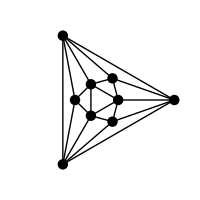
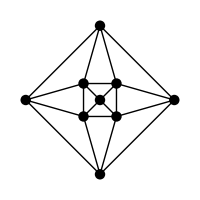
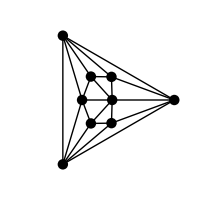
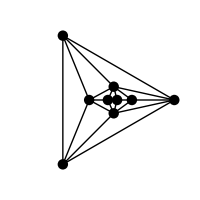
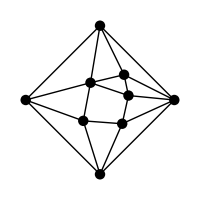
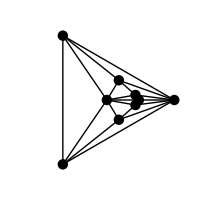
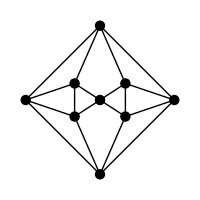

```mathematica
drawGraph/@planarGraphDials[5]
```

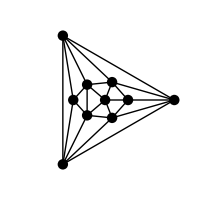
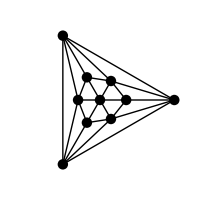
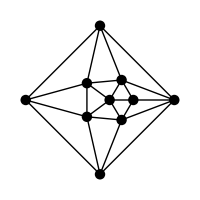
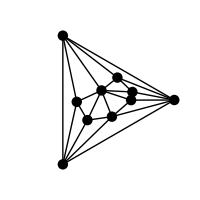
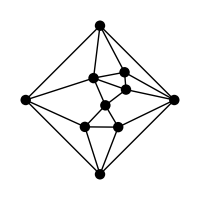
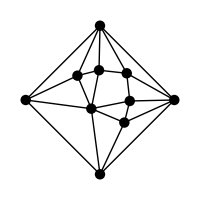
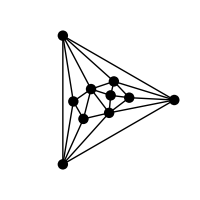
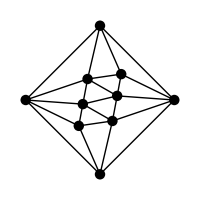

```mathematica
drawGraph/@planarGraphDials[6]
```

Example usage of the optional second argument: All of the following are different drawings of the same graph (choosing different triangular faces to be external)

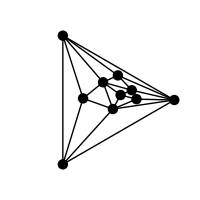
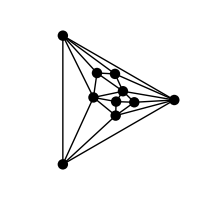
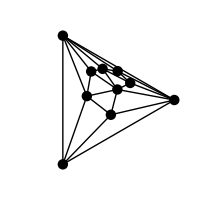
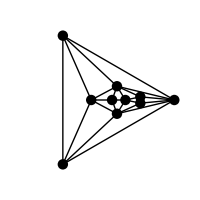
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
drawGraph[planarGraphDials[6][[-7]],#]&/@Range[5]
```

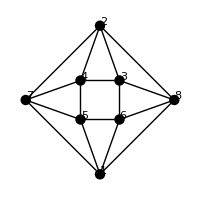

```mathematica
drawGraph[planarGraphDials[4][[2]],{},True]
```

# Extraction

### Functions

```mathematica
SetAttributes[ProdToList,Listable]
ProdToList[x_]:=Block[{Times=List,Power=Table},If[Head[x]===List,Flatten@x,{x}]]
```

```mathematica
ExpToDenominatorGraph[x_List]:=ExpToDenominatorGraph[#]&/@x
ExpToDenominatorGraph[x_List,v_]:=ExpToDenominatorGraph[#,v]&/@x
ExpToDenominatorGraph[t_]:=Graph[UndirectedEdge@@@ProdToList@Denominator[t],VertexLabels->"Name"]
ExpToDenominatorGraph[t_,vert_List]:=Module[{temp},
temp=Denominator[t];
If[temp===1,Graph[vert,{}],
Graph[vert,UndirectedEdge@@@ProdToList@temp,VertexLabels->"Name"]]
]
```

```mathematica
ExpToNumeratorGraph[x_List]:=ExpToDenominatorGraph[#]&/@x
ExpToNumeratorGraph[x_List,v_]:=ExpToDenominatorGraph[#,v]&/@x
ExpToNumeratorGraph[t_]:=If[Numerator[t]===1,Graph[VertexList@ExpToDenominatorGraph[t],{}],Graph[VertexList@ExpToDenominatorGraph[t],UndirectedEdge@@@ProdToList@Numerator[t]]]
ExpToNumeratorGraph[t_,vert_List]:=Module[{temp},
temp=Denominator[t];
If[temp===1,Graph[vert,{}],
Graph[vert,UndirectedEdge@@@ProdToList@temp,VertexLabels->"Name"]]
]
```

```mathematica
Clear[denGraph]
denGraph[l_]:=denGraph[l]=ExpToDenominatorGraph/@fGraphList[l]
```

```mathematica
Clear[numGraph]
numGraph[l_]:=numGraph[l]=ExpToNumeratorGraph/@fGraphList[l]
```

```mathematica
(*Gives the edges of a graph as String in the notation of the phyton library networkx, that is a list of tuples*)
edgeListNX[graph_]:=StringReplace[ StringReplace[ToString[EdgeList[graph]/. UndirectedEdge->List],{"{"->"(","}"->")"}],{"(("->"[(","))"->")]"}]
```

```mathematica
graphDataCSV[l_]:=Module[{data,csv},
data =Transpose[{amplitudeCoefficients[l],edgeListNX/@denGraph[l],edgeListNX/@numGraph[l]}];
csv=Prepend[data,{"COEFFICIENTS","DEN_EDGES","NUM_EDGES"}];
Export["graph_data_"<>ToString[l]<>".csv",csv]
]
```

### Extraction

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/gabriele/Documents/GitHub/ML-correlator/Tree classifier for graphs

```mathematica
graphDataCSV[6]
```

graph_data_6.csv

```mathematica
denGraph[6]
```

{{}}